```mathematica
Clear["`*"]
corrfunc[datin_,plusin_]:=Module[{datnew,μ,μ2,dat},
datnew=datin*0;
dat=datin;
Do[
If[n+plusin≤Length[datin],datnew[[n]]=datin[[n+plusin]],datnew[[n]]=datin[[n+plusin-Length[datin]]]];
,{n,1,Length[datin]}
];
datnew=datnew[[1;;Length[datin]-plusin]];
dat=dat[[1;;Length[datin]-plusin]];
μ=Mean[dat];
μ2=Mean[dat^2];
(Mean[datnew*dat]-μ2)/μ2
]
SetDirectory[NotebookDirectory[]];
data=Transpose[Import["he4/he4lin.dmc10000_3.dat"]][[4]];
```

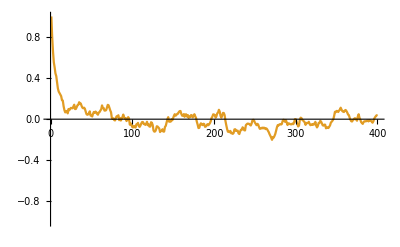

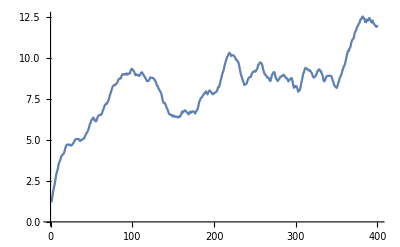

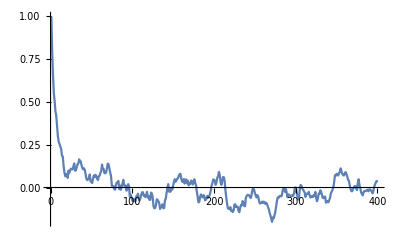

```mathematica
max=400;
corr=Range[1,max]*0;
Do[
corr[[n]]=corrfunc[data,n]
,{n,max}
]
datMat=Transpose[{Range[1,max],CorrelationFunction[data,{1,max}]/CorrelationFunction[data,1]}];
datme=Transpose[{Range[1,max],corr*5400+1}];
ListPlot[{datme,datMat},Joined->True,PlotRange->{-1,1}]
ListPlot[datme,Joined->True,PlotRange->All]
ListPlot[datMat,Joined->True,PlotRange->All]
```

```mathematica
plus=1;
dat={1,2,1,3,2,1,1,3,1,2,1,1,3,2,3,2};
dat={10,9,8,5,6,3,4,2,1,2,1,3,2,1,3,1};
CorrelationFunction[dat,plus]//N
corrfunc[dat,plus]*5400+1//N
```

0.663255

-916.26

```mathematica
corrfunc[{a,b},1]//FullSimplify
AbsoluteCorrelationFunction[{a,b},1]
%//FullSimplify
```

-(a-b)^2/(a+b)^2

(a b)/2

(a b)/2

```mathematica
corrfunc[{a,b},1]
%//FullSimplify
```

(2 (b+1/2 (-a^2-b^2)))/(a^2+b^2)

-1+(2 b)/(a^2+b^2)

```mathematica
(-a+b)/(2 (a-b))//FullSimplify
```

-1/2

```mathematica
-(a-2 b+c)^2/((6 a-3 (b+c)) a-3 ((a-2 b+c) b+(a+b-2 c) c))//Expand//FullSimplify
```

-(a-2 b+c)^2/(6 (a^2+b^2-b c+c^2-a (b+c)))

```mathematica
CorrelationFunction[data,1]/
```

0.7144